# The Notebook paths.nb

In this notebook we arrive at the result in Eq. (11), which is the generalized entanglement measure for the intermediate case of path superposition with non-negligible gaussian width. The calculation proceeds as follows: (1) defining the non-relativistic action, (2) finding the classical solutions of the system, (3) computing the gaussian integrals in Eq. (9), (4) calculating for this wavefunction the generalized entanglement measure [Swain et al, Phys. Rev. A 105, 052441 (2022)] defined in Eq. (28), to get Eq. (11).

```mathematica
<<VariationalMethods`

$Assumptions =  {m>0, d>0,ω>0,ξ>0, t>0, ϕ>0 , ϵ>0 ,Ω>0 ,ti>0,y1∈Reals,y2∈Reals,y1p∈Reals,y2p∈Reals,4 ϵ^2 ϕ<1,trp>=0,ξ1∈Reals,ξ2∈Reals,s1i∈Reals,s2i∈Reals,s1j∈Reals,s2j∈Reals,s1k∈Reals,s2k∈Reals,s1l∈Reals,s2l∈Reals};

(*defining the dimensionless quantities ϵ, ϕ and Ω which fully define the problem.*)
ℏ=ϵ^2 d^2 m ω; (*ϵ = α/d is a measure of the "quantumness" of the particles*)
G = ϕ ℏ  d ω /(m^2 ) ; (*ϕ = Gm^2/ℏωd is a measure of the effect of gravity on the system*)
c= d ω/(Ω ); (*Ω = ωd/c is a measure of the effect of retardation in the system*)

α=Sqrt[ℏ/(m ω)]; (*the width of the gaussian*)

(*a function calculating an integral of the form fPre Exp[fExp], where fPre is a polynomial and fExp a 2nd order polynomial. Taken from https://mathematica.stackexchange.com/a/6846.*)
gaussMoment[fPre_,fExp_,vars_]:=Module[{coeff,dist,ai,μ,norm},coeff=CoefficientArrays[fExp,vars,"Symmetric"->True];
ai=Inverse[2 coeff[[3]]];
μ=-ai.coeff[[2]];
dist=MultinormalDistribution[μ,-ai];
norm=1/PDF[dist,vars]/. Thread[vars->μ];
norm Exp[1/2 coeff[[2]].μ+coeff[[1]]] Distribute@Expectation[fPre,vars\[Distributed]dist]]

(*functions replacing coefficients of given polynomials with single symbols. This makes mathematica work much faster.*)
myMatrix[symb_,d1_,d2_,d3_,d4_]:=Table[Subscript[symb,i1,i2,i3,i4],{i1,d1},{i2,d2},{i3,d3},{i4,d4}];
symbolize[poly_,vars2_,symb_]:=Module[{lst,flst,symbolized,dims,symbCoeffs},
lst=CoefficientList[poly,vars2];
dims = Dimensions[lst];
symbCoeffs = myMatrix[symb,dims[[1]],dims[[2]],dims[[3]],dims[[4]]];
Do[
If[lst[[i1,i2,i3,i4]]==0,symbCoeffs[[i1,i2,i3,i4]]=0];
,{i1,1,dims[[1]]},{i2,1,dims[[2]]},{i3,1,dims[[3]]},{i4,1,dims[[4]]}];
symbolized = Internal`FromCoefficientList[symbCoeffs,vars2];
symbolized
];

(*a function wrapping gaussMoment, replacing coefficients with symbols before integrating.*)
myGauss[fPre_,fExp_,vars1_]:=Module[{a0exp,a0pre,aexp,apre,sympre,symexp,res},
a0exp = CoefficientList[fExp,vars];
symexp=symbolize[fExp,vars,aexp];
a0pre = CoefficientList[fPre,vars];
sympre=symbolize[fPre,vars,apre];
res = gaussMoment[ sympre  ,symexp,vars1]/.{aexp->a0exp,apre->a0pre,Subscript->Part};
res
]

(*operations on complex numbers done in a custom way which for some reason works faster.*)
myRe[var_] := Module[{var1,var1C,re,im}, 
var1 = var//ComplexExpand//Evaluate;
var1C = var1//Conjugate//Refine;
re = (var1+var1C)/2 // Simplify;
re 
]

myIm[var_] := Module[{var1,var1C,re,im}, 
var1 = var//ComplexExpand//Evaluate;
var1C = var1//Conjugate//Refine;
im = -ⅈ(var1-var1C)/2 // Simplify;
im 
]

myConj[var_] := Module[{var1,var1C,re,im}, 
var1 = var//ComplexExpand//Evaluate;
var1C = var1//Conjugate//Refine;
var1C
]

(*the series expansion to second order in ϵ and zeroth order in Ω. The second function is for quantities which will be taken with a square root later.*)
mySeries[expr_]:=Series[ expr,{Ω,0,0},{ϵ,0,2}]//Normal; 
mySeriesSq[expr_]:=Series[expr,{Ω,0,0},{ϵ,0,4}]//Normal;
```

## Action

We define action of the gravitational interaction: SGhb = S_G / ℏ. This is the Newtonian potential, as we work in the non-relativistic limit in this calculation. The functions q1, q2 are the variables for the lagrangian and action.

```mathematica
LG12= (G m^2  /2)/(d+α q1[ti]+α q2[ti])/ℏ      //mySeries // Simplify ;
LGhb=LG12 + (LG12/.{q1->q2,q2->q1}) //mySeries //Simplify
SGhb = Integrate[ LGhb,{ti,0,t}] ;
```

ϕ ω (1-ϵ (q1[ti]+q2[ti])+ϵ^2 (q1[ti]+q2[ti])^2)

The free, uncoupled action: Sunc =   Σ_(a=1,2) S_a / ℏ:

```mathematica
Lunc =( m(α q1'[ti])^2/2+ m(α q2'[ti])^2/2)/ℏ //mySeries//Simplify
Sunc= Integrate[ Lunc,{ti,0,t}] ;
```

(q1'[ti]^2+q2'[ti]^2)/(2 ω)

Now that we have defined the action, we proceed to finding the solution to the classical equations of motion, which we will use for the stationary-phase approximation in Eq. (9).

## Classical Solutions

We find the classical trajectories of the particles for initial locations y1p, y2p = y'_1/ α , y'_2 / α and final locations y1, y2 = y_1/ α , y_2/ α. Here, the y’s are in units of α, the gaussian’s width. We do it by solving the system under the second order approximation in ϵ. The problem becomes two harmonic oscillators with some frequency trp×ω, which are coupled by another spring, which is gravity. The variable trp is just a bookkeeping variable which will be taken to zero to achieve the trajectories of the two otherwise free particles coupled by gravity.

```mathematica
L[ti]:=(LGhb+Lunc) ;
L[ti]//Simplify
```

ϕ ω (1-ϵ (q1[ti]+q2[ti])+ϵ^2 (q1[ti]+q2[ti])^2)+(q1'[ti]^2+q2'[ti]^2)/(2 ω)

```mathematica
eqs=EulerEquations[L[ti],{q1[ti],q2[ti]},ti] //Expand (*the classical equations of motion*)
```

{-ϵ ϕ ω+2 ϵ^2 ϕ ω q1[ti]+2 ϵ^2 ϕ ω q2[ti]-q1''[ti]/ω==0,-ϵ ϕ ω+2 ϵ^2 ϕ ω q1[ti]+2 ϵ^2 ϕ ω q2[ti]-q2''[ti]/ω==0}

```mathematica
sol = DSolve[{eqs[[1]],eqs[[2]],q1[0]==y1p,q2[0]==y2p,q1[t]==y1,q2[t]==y2},{q1[ti],q2[ti]},{ti}]//Simplify;(*their solution*)
```

```mathematica
x1[time_]:= q1[ti] /.sol[[1]]/.ti->time;
x2[time_]:= q2[ti] /.sol[[1]]/.ti->time;
x1[ti]
x2[ti]
```

1/(4 (-1+ⅇ^(4 t ϵ √ϕ ω)) t ϵ)ⅇ^(-2 ti ϵ √ϕ ω) (-ⅇ^(2 t ϵ √ϕ ω) t (-1+2 y1 ϵ+2 y2 ϵ)+ⅇ^(2 (t+2 ti) ϵ √ϕ ω) t (-1+2 y1 ϵ+2 y2 ϵ)+ⅇ^(4 t ϵ √ϕ ω) t (-1+2 y1p ϵ+2 y2p ϵ)-ⅇ^(4 ti ϵ √ϕ ω) t (-1+2 y1p ϵ+2 y2p ϵ)-ⅇ^(2 ti ϵ √ϕ ω) (2 ti (y1-y1p-y2+y2p) ϵ+t (1+2 y1p ϵ-2 y2p ϵ))+ⅇ^(2 (2 t+ti) ϵ √ϕ ω) (2 ti (y1-y1p-y2+y2p) ϵ+t (1+2 y1p ϵ-2 y2p ϵ)))

1/(4 (-1+ⅇ^(4 t ϵ √ϕ ω)) t ϵ)ⅇ^(-2 ti ϵ √ϕ ω) (-ⅇ^(2 t ϵ √ϕ ω) t (-1+2 y1 ϵ+2 y2 ϵ)+ⅇ^(2 (t+2 ti) ϵ √ϕ ω) t (-1+2 y1 ϵ+2 y2 ϵ)+ⅇ^(4 t ϵ √ϕ ω) t (-1+2 y1p ϵ+2 y2p ϵ)-ⅇ^(4 ti ϵ √ϕ ω) t (-1+2 y1p ϵ+2 y2p ϵ)+ⅇ^(2 ti ϵ √ϕ ω) (2 ti (y1-y1p-y2+y2p) ϵ+t (-1+2 y1p ϵ-2 y2p ϵ))+ⅇ^(2 (2 t+ti) ϵ √ϕ ω) (2 ti (-y1+y1p+y2-y2p) ϵ+t (1-2 y1p ϵ+2 y2p ϵ)))

Sanity check: initial and final locations

```mathematica
x1[0]//mySeries // Simplify
x2[0]//mySeries // Simplify
x1[t]//mySeries // Simplify
x2[t]//mySeries // Simplify
```

y1p

y2p

y1

y2

sanity check: check that the solution actually solves the classical equation

```mathematica
L[ti]:=LGhb+Lunc;
EulerEquations[L[ti],{q1[ti],q2[ti]},ti] /.{q1->x1,q2->x2} // mySeries //Simplify
```

{True,True}

## Wavefunction

We would now like to compute the wavefunction ψ^(~ fi)(y1, y2) as given in Eq. (9). We start with achieving the expression for the on-shell ( = stationary-phase approximated) action (S^~)_a + (S^~)_G, here Shb.

```mathematica
Lhb =  LGhb+Lunc/.{q1->x1,q2->x2} //mySeries//Simplify;
Shb1 = Integrate[Lhb  ,{ti,0,t}] ;
Shb =Shb1 - (Shb1/.{y1->0,y2->0,y1p->0,y2p->0})//Expand // Refine//Simplify
```

1/(6 t ω)(3 y2^2-6 y2 y2p+3 y2p^2-3 t^2 y2 ϵ ϕ ω^2-3 t^2 y2p ϵ ϕ ω^2+2 t^2 y2^2 ϵ^2 ϕ ω^2+2 t^2 y2 y2p ϵ^2 ϕ ω^2+2 t^2 y2p^2 ϵ^2 ϕ ω^2+t^2 y1 ϵ (-3+4 y2 ϵ+2 y2p ϵ) ϕ ω^2+t^2 y1p ϵ (-3+2 y2 ϵ+4 y2p ϵ) ϕ ω^2+2 y1 y1p (-3+t^2 ϵ^2 ϕ ω^2)+y1^2 (3+2 t^2 ϵ^2 ϕ ω^2)+y1p^2 (3+2 t^2 ϵ^2 ϕ ω^2))

We now solve the y1p and y2p integrals while also performing the approximations. We denote for any function f the parts fExp and fPre such that f(x) = fPre(x) × ⅇ^(fExp(x)).
The initial state is a sum of four gaussians with ξ1, ξ2 = ± β /α. We therefore perform one calculation (the variable summand) and then use it four times with the appropriate replacements of ξ1, ξ2.

```mathematica
vars={y1,y2,y1p,y2p};
summand =  Exp[ -(y1p-ξ1)^2/2-(y2p-ξ2)^2/2] * (ⅈ/((-ⅈ+ω t) (3+3 ⅈ ω t+4 ϵ^2 ϕ (ω t)^2)))^(-1/2); (*four of these make up the initial state. prefactor added for a simpler expression later*)
```

```mathematica
wf4vars=summand Exp[ⅈ  Shb]//mySeriesSq//Simplify; (*the integrand in Eq. (9).*)
wf4varsExp = Exponent[wf4vars,ⅇ]//mySeries//Simplify;
wf4varsPre = wf4vars Exp[-wf4varsExp] //mySeriesSq// Simplify;
wf =myGauss[    wf4varsPre ,wf4varsExp,{y1p,y2p}]//mySeriesSq//Simplify; (*This is ψ^(~ fi)(y1, y2)*)
wfExp= Exponent[wf,ⅇ]//mySeries//Simplify;
wfPre= wf Exp[-wfExp] //mySeriesSq// Simplify;
wfExpC = wfExp//myConj // Simplify; (*complex conjugate*)
wfPreC =wfPre//myConj//Simplify;
```

calculate the norm squared normsq of the state, integrating each separate exponent separately using our myGauss function:

```mathematica
wfExp0={wfExp/.{ξ1->ξ,ξ2->ξ},wfExp/.{ξ1->-ξ,ξ2->ξ},wfExp/.{ξ1->ξ,ξ2->-ξ},wfExp/.{ξ1->-ξ,ξ2->-ξ}};
wfExpC0={wfExpC/.{ξ1->ξ,ξ2->ξ},wfExpC/.{ξ1->-ξ,ξ2->ξ},wfExpC/.{ξ1->ξ,ξ2->-ξ},wfExpC/.{ξ1->-ξ,ξ2->-ξ}};
wfPre0={wfPre/.{ξ1->ξ,ξ2->ξ},wfPre/.{ξ1->-ξ,ξ2->ξ},wfPre/.{ξ1->ξ,ξ2->-ξ},wfPre/.{ξ1->-ξ,ξ2->-ξ}};
wfPreC0={wfPreC/.{ξ1->ξ,ξ2->ξ},wfPreC/.{ξ1->-ξ,ξ2->ξ},wfPreC/.{ξ1->ξ,ξ2->-ξ},wfPreC/.{ξ1->-ξ,ξ2->-ξ}};

normsq = 0;
Do[
preee = wfPreC0[[i]]wfPre0[[j]]//mySeriesSq;
preee = preee //Simplify;
res=myGauss[preee,wfExpC0[[i]]+wfExp0[[j]],{y1,y2}];
res = res //mySeriesSq;
res = res //Simplify;
If[i!=j,res=2 myRe[res];];
normsq+=res;
,{i,1,Length[wfExp0]},{j,i,Length[wfExp0]}]
normsq=normsq  // Simplify;
```

## Generalized Entanglement Measure

we now calculate the entanglement measure in Eq. (28) after replacing the norm square in the formula by multiplication with the conjugate:
 |∫ψ(y1,y2) ψ*(y'1,y2)ⅆy2 |^2=∫ψ*(y1,y2) ψ(y'1,y2)ψ(y1,y'2) ψ*(y'1,y'2)ⅆy2 ⅆy'2
 each ψ contains 4 elements, so we have 16 elements in the integrand. We calculate only once (variable summand2), and then sum over the 16 possible choices of the signs in the ξ’s.

```mathematica
(*each of the four multipicants inside the integral above is slightly different in where is the ' and whether it is conjugate*)
wfPre1p = wfPre/.y1->y1p;
wfExp1p=wfExp /.y1->y1p;
wfPre2p = wfPre/.y2->y2p;
wfExp2p=wfExp /.y2->y2p;
wfPreC12p = wfPreC/.{y1->y1p,y2->y2p};
wfExpC12p=wfExpC /.{y1->y1p,y2->y2p};

(*we again get to the form f(x)=fPre(x)×ⅇ^(fExp(x)) before we calculate the integral using myGauss*)
thisPre = (wfPre1p/.{ξ1->s1i ξ,ξ2->s2i ξ}) (wfPreC/.{ξ1->s1j ξ,ξ2->s2j ξ})(wfPreC12p/.{ξ1->s1k ξ,ξ2->s2k ξ})(wfPre2p/.{ξ1->s1l ξ,ξ2->s2l ξ}) //mySeriesSq//Simplify;
Print["pre series"];
thisExp=(wfExp1p/.{ξ1->s1i ξ,ξ2->s2i ξ}) +(wfExpC/.{ξ1->s1j ξ,ξ2->s2j ξ})+(wfExpC12p/.{ξ1->s1k ξ,ξ2->s2k ξ})+(wfExp2p/.{ξ1->s1l ξ,ξ2->s2l ξ})//Simplify;
Print["exp simp"];
summand2=myGauss[thisPre,thisExp,{y1,y2,y1p,y2p}];
Print["int"];
summand2=summand2/normsq^2// mySeriesSq//Simplify; (*normalize*)
Print["int ser"];
summand2=summand2//Simplify;
Print["int simp"];
```

pre series

exp simp

int

int ser

int simp

now sum over the 16 elements:

```mathematica
sum = Sum[ summand2,{s1i,{-1,1}},{s2i,{-1,1}},{s1j,{-1,1}},{s2j,{-1,1}},{s1k,{-1,1}},{s2k,{-1,1}},{s1l,{-1,1}},{s2l,{-1,1}}]//Simplify;
```

finally, the generalized entanglement measure (Eq. 28) is:

```mathematica
gem = Sqrt[2(1-sum)]  //Expand //Simplify
```

(1/(3 (1+ⅇ^(ξ^2))))2 t ϵ^2 ϕ ω √(9+3 t^2 (1-3 ξ^2) ω^2+t^4 (1-2 ξ^2)^2 ω^4+ⅇ^(2 ξ^2) (9+36 ξ^4+3 t^2 ω^2+t^4 ω^4+9 ξ^2 (4+t^2 ω^2))+2 ⅇ^(ξ^2) (9+3 t^2 ω^2-9 t^2 ξ^4 ω^2+t^4 ω^4-2 ξ^2 (-9+t^4 ω^4)))

find a nicer representation (Eq. 11) with order 1 functions (Eq. 29):

```mathematica
coefflist=(gem/(2 t ϵ^2 ϕ ω))^2 /.{ξ->x,ω->1}// CoefficientList[#,t]& ;
```

```mathematica
f0=coefflist[[1]]-4x^2(1+x^2) //Simplify
```

(1+ⅇ^(2 x^2)-4 x^2-4 x^4+ⅇ^(x^2) (2-4 x^2-8 x^4))/(1+ⅇ^(x^2))^2

```mathematica
f2=3coefflist[[3]]-3 x^2 //Simplify
```

(1+ⅇ^(2 x^2)-6 x^2+ⅇ^(x^2) (2-6 x^2-6 x^4))/(1+ⅇ^(x^2))^2

```mathematica
f4=9coefflist[[5]] //Simplify
```

(1+ⅇ^(x^2)-2 x^2)^2/(1+ⅇ^(x^2))^2

```mathematica
gem^2 -( 2 t ϵ^2 ϕ ω Sqrt[f0+4x^2(1+x^2)+f2 (ω t)^2/3+x^2 (ω t)^2 + f4 (ω t)^4 / 9])^2/.ξ->x//FullSimplify (*a sanity check: this should be zero if Eq. (11) really equals to our result from gem above.*)
```

0

Plot the functions:

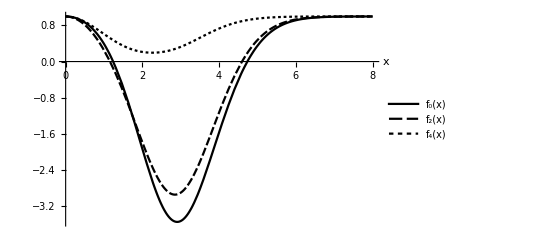

```mathematica
Plot[{(1+ⅇ^(2 x^2)-4 x^2-4 x^4+ⅇ^(x^2) (2-4 x^2-8 x^4))/(1+ⅇ^(x^2))^2/.x->xx/2,(1+ⅇ^(2 x^2)-6 x^2+ⅇ^(x^2) (2-6 x^2-6 x^4))/(1+ⅇ^(x^2))^2/.x->xx/2,(1+ⅇ^(x^2)-2 x^2)^2/(1+ⅇ^(x^2))^2/.x->xx/2},{xx,0,8},PlotLegends->Placed[{"f_0(x)","f_2(x)","f_4(x)"},{Right,Bottom}],PlotTheme->"Monochrome",AxesLabel->{"x"}]  (*the x is divided by two because in the paper the distance between the paths is β and in this notebook it is 2β.*)
```